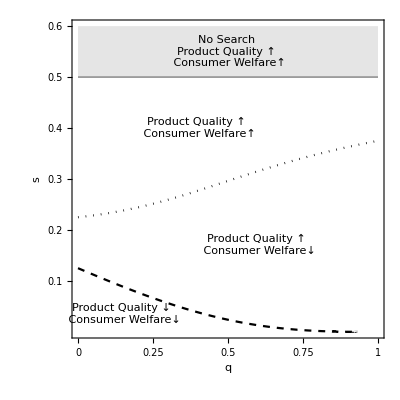

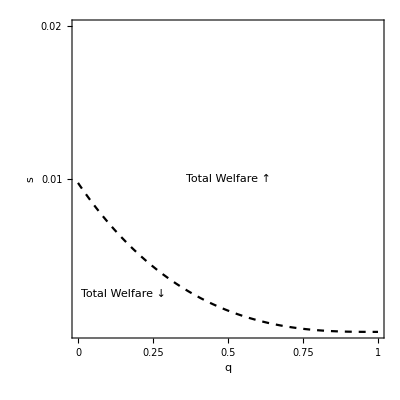

```mathematica
Clear["Global`*"]
ClearAll[Subscript]

(*Model primitives*)
F[z_]:=z;
f[z_]:=D[F[z],z];
ϵ̲=0;
ϵ̄=1;

(*Distribution of the second good quality Y conditional on observed quality X of the first one in the region Y>X*)
g[y_,x_]:=((1-p)(1-F[x]))/((1-p)(1-F[x])+p F[x])f[y]/(1-F[x])/.p->(1+q)/2;

(*Probability of visiting the second firm*)
Pr[z_]:=(1-q)/2(1-F[z])^2;

(*Incremental utility of one extra search*)
ΔU[z_]:=FullSimplify[∫_z^(ϵ̄) (y-z)g[y,z]ⅆy];

(*Product Quality and Search Expenditures*)
MQ[z_] :=(1-Pr[z])∫_(ϵ̲)^(ϵ̄) ϵ 2f[ϵ]F[ϵ]ⅆϵ+ Pr[z]∫_(ϵ̲)^(ϵ̄) ϵ 2f[ϵ](1-F[ϵ])ⅆϵ;
SE[z_]:=s(1+(1+q)/2 F[z]^2+(1-q)/2(1-(1-F[z])^2));

(*Demand and Price*)
Demand[p_,P_,z_]:=1/2(1+F[z])(1-F[z+p-P])+∫_(ϵ̲)^(z+p-P) f[ϵ]F[ϵ-p+P]ⅆϵ;
Price[z_]:=p/.Solve[p==FullSimplify[-Demand[p,p,z]/(D[Demand[p,P,z],p]/.P->p)],p]⟦1⟧;

(*Derivatives of main expressions*)
DPr[z_]:=FullSimplify[D[Pr[z[q]],q]/.z[q]->z];
DMQ[z_]:=DPr[z](∫_(ϵ̲)^(ϵ̄) ϵ 2f[ϵ](1-F[ϵ])ⅆϵ-∫_(ϵ̲)^(ϵ̄) ϵ 2f[ϵ]F[ϵ]ⅆϵ);
DSE[z_]:=Simplify[D[SE[z[q]],q]/.z[q]->z];
DTS[z_]:=DMQ[z]-DSE[z];

DPrice[z_]:=Simplify[D[Price[z[q]],q]/.z[q]->z];
DCS[z_]:=DTS[z]-DPrice[z];

(*Computation of X and (∂X)/(∂q)*)
X=Normal[z/.Solve[s==ΔU[z],z,Reals]⟦1⟧];
ϕ'[q]=FullSimplify[z'[q]/.Solve[FullSimplify[0==D[ΔU[z[q]],q]],z'[q]]⟦1⟧/.z[q]->ϕ];

(*Graphs*)
(*Contourplots DMQ=0, DCS=0*)
FullSimplify[Simplify[DMQ[ϕ]/.ϕ->X]];
plot1=ContourPlot[{%==0},{q,0,1},{s,0,1/2},PlotPoints->200,FrameLabel->{"q",Rotate["s",-90Degree]},BoundaryStyle->{Black,Thick},PlotRange->{{0,1},{0,0.6}},ContourStyle->{{Black,Dashed}},FrameTicks->{{0,0.25,0.5,0.75,1},{.1,.2,.3,.4,.5,.6}},FrameTicksStyle->{{Black,White},{Black,White}}];
FullSimplify[Simplify[DCS[ϕ]/.ϕ->X]];
plot2=ContourPlot[{%==0},{q,0,1},{s,0,1/2},PlotPoints->100,FrameLabel->{"q",Rotate["s",-90Degree]},BoundaryStyle->{Black,Thick},PlotRange->{{0,1},{0,0.6}},ContourStyle->{{Black,Dotted}}];
plot3=Plot[{1/2},{q,0,1},PlotRange->{{0,1},{0,0.6}},PlotStyle->{{Gray,Thin}},Filling->Top];
text=Graphics[{Text["Product Quality ↓ \n Consumer Welfare↓",{0.15,0.035}],
Text["Product Quality ↑ \n Consumer Welfare↓",{0.6,0.17}],
Text["Product Quality ↑ \n Consumer Welfare↑",{0.4,0.4}],
Text["No Search \nProduct Quality ↑ \n Consumer Welfare↑",{0.5,0.55}]}];
Show[plot1,plot2,plot3(*,plot4*),text]

(*Contourplot DTS=0*)
s/.Normal[Solve[(DTS[ϕ]/.ϕ->X)==0&&0<q<1&&0<s<1/2,s]]⟦1⟧;
plot21=Plot[%,{q,0,1},PlotRange->{{0,1},{0,0.02}},PlotStyle->{{Dashed,Black}},Axes->False,Frame->True,FrameLabel->{"q",Rotate["s",-90Degree]},PlotRange->{{0,1},{0,0.6}},FrameTicks->{{0,0.25,0.5,0.75,1},{0.01,0.02}},FrameTicksStyle->{{Black,White},{Black,White}},AspectRatio->1];
text2=Graphics[{Text["Total Welfare ↓",{0.15,0.0025}],Text["Total Welfare ↑",{0.5,0.01}]}];
Show[plot21,text2]
```